## Prelab problems

#### 1.

```mathematica
?For
```

For[start,test,incr,body] executes start, then repeatedly evaluates body and incr until test fails to give True.

```mathematica
?If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

```mathematica
?While
```

While[test,body] evaluates test, then body, repetitively, until test first fails to give True.

#### 2.

```mathematica
Sin[x]  ≃Sum[(x^(2n+1)*(-1)^n)/Factorial[2n+1], n]
```

#### 3.

```mathematica
?Timing
```

Timing[expr] evaluates expr, and returns a list of the time in seconds used, together with the result obtained.

```mathematica
Timing[Table[0,{i, 0, 10000000}]]
```

{0.150894,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9999857,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
 |  |  |  |

#### 4.

```mathematica
sinetable = Table[{x,Sin[2 Pi x]},{x,0,1,.1}]
```

{{0.,0.},{0.1,0.587785},{0.2,0.951057},{0.3,0.951057},{0.4,0.587785},{0.5,1.22465×10^-16},{0.6,-0.587785},{0.7,-0.951057},{0.8,-0.951057},{0.9,-0.587785},{1.,-2.44929×10^-16}}

```mathematica
FindFit[sinetable,a*Sin[b*x+c],{a,b, c},x]
```

{a→1.,b→6.28319,c→-2.4603×10^-13}

```mathematica
?FindFit
```

FindFit[data,expr,pars,vars] finds numerical values of the parameters pars that make expr give a best fit to data as a function of vars. 
FindFit[data,{expr,cons},pars,vars] finds a best fit subject to the parameter constraints cons.

## Lab Questions

#### 1.

```mathematica
Sine[theta_,Nterms_] := Sum[(theta^(2n+1)*(-1)^n)/Factorial[2n+1], {n,0,Nterms}]
```

```mathematica
Sine[1,10]
```

42991545423991633141/51090942171709440000

```mathematica
Sine[Pi,10]
```

π-π^3/6+π^5/120-π^7/5040+π^9/362880-π^11/39916800+π^13/6227020800-π^15/1307674368000+π^17/355687428096000-π^19/121645100408832000+π^21/51090942171709440000

```mathematica
Sine[Pi/2., 10]
```

1.

```mathematica
theta := 1
```

```mathematica
Sine[theta,1]
```

5/6

```mathematica
Sine[theta,2]
```

101/120

```mathematica
Sine[theta,3]
```

4241/5040

```mathematica
Sine[theta,4]
```

305353/362880

```mathematica
Sine[theta,5]
```

33588829/39916800

```mathematica
sinetable2 = Table[Sine[1,n], {n, 5}]
```

{5/6,101/120,4241/5040,305353/362880,33588829/39916800}

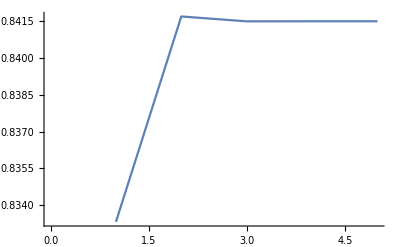

```mathematica
ListLinePlot[sinetable2]
```

#### 2.

```mathematica
DotProduct[vec1_,vec2_] :=
If [Length[vec1] ≠ Length[vec2],
	Return["Length mismatch"],
Return[Sum[vec1[[i]]*vec2[[i]], {i, Length[vec1]}]]]
```

```mathematica
DotProduct[{1,1,1},{2,2,2}]
```

6

```mathematica
a = {1.,2.,3.,4.,5.};
b= {2.,4.,6.,8.,10.};
a.b
DotProduct[a,b]
```

110.

110.

```mathematica
a = {1.,2.,3.,4.,5.};
b= {2.,4.,6.,8.,10.,11.};
a.b
DotProduct[a,b]
```

Dot::dotsh: Tensors {1.,2.,3.,4.,5.} and {2.,4.,6.,8.,10.,11.} have incompatible shapes.

{1.,2.,3.,4.,5.}.{2.,4.,6.,8.,10.,11.}

Length mismatch

#### 3.

```mathematica
RandomDot[Nvals_] := Module[{a,b},
a = Table[RandomReal[{-1.,1.}], Nvals];
b = Table[RandomReal[{-1.,1.}], Nvals];
Return[DotProduct[a,b]]
]
```

```mathematica
RandomDot[10]
```

0.193407

```mathematica
RandomDot[10]
```

```mathematica
-0.318563520552406
```

#### 4.

```mathematica
Timing[RandomDot[10^4]]
```

{0.009879,3.52769}

```mathematica
timetable = Table[{j,Timing[RandomDot[j*10^4]][[1]]}, {j, 10}];
```

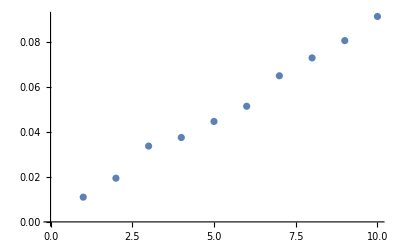

```mathematica
ListPlot[timetable]
```

```mathematica
?Clear
```

Clear[symbol_1,symbol_2,…] clears values and definitions for the symbol_i. 
Clear[form,form,…] clears values and definitions for all symbols whose names match any of the string patterns form_i.

```mathematica
Clear[a,b]
FindFit[timetable, a x + b, {a,b}, x]
```

{a→0.00942884,b→0.00109787}

```mathematica
?Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

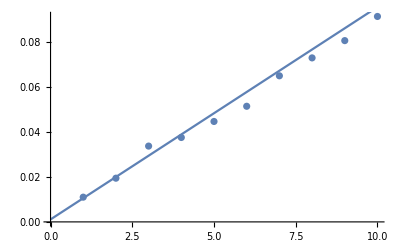

```mathematica
Show[ListPlot[timetable], Plot[0.00942884 x + 0.00109787, {x, 0, 50}]]
```